```mathematica
h[x_]:=Piecewise[{{1+Subscript[c, 0,1] x+Subscript[c, 0,2] x^2, 0≤x≤1}, {Subscript[c, 1,1](x-1)+Subscript[c, 1,2](x-1)^2, 1<x≤2}, {Subscript[c, 2,1](x-2)+Subscript[c, 2,2](x-2)^2, 2<x≤3}, {0, True}}];
f[x_]:=h[Abs[x]];
AllVars={Subscript[c, 0,1],Subscript[c, 0,2],Subscript[c, 1,1],Subscript[c, 1,2],Subscript[c, 2,1],Subscript[c, 2,2]};
```

```mathematica
(*Interpolant constraints*)
I1=f[1]
I2=f[2]
I3=f[3]
```

1+c_(0,1)+c_(0,2)

c_(1,1)+c_(1,2)

c_(2,1)+c_(2,2)

```mathematica
(*Partition of unity and linear term*)
T0=CoefficientList[FullSimplify[∑_(k=-2)^3 f[x-k],x>0&&x<1],x]
T1=CoefficientList[FullSimplify[∑_(k=-2)^3 k f[x-k],x>0&&x<1],x]
```

{2+c_(0,1)+c_(0,2)+c_(1,1)+c_(1,2)+c_(2,1)+c_(2,2),-2 c_(0,2)-2 (c_(1,2)+c_(2,2)),2 c_(0,2)+2 (c_(1,2)+c_(2,2))}

{1+c_(0,1)+c_(0,2)+2 c_(1,1)+2 c_(1,2)+3 c_(2,1)+3 c_(2,2),-c_(0,1)-2 c_(0,2)-3 c_(1,1)-4 c_(1,2)-5 c_(2,1)-6 c_(2,2),c_(0,2)+c_(1,2)+c_(2,2)}

```mathematica
GenSols=Solve[{
	I1==0,
	I2==0,
	I3==0,
	T0[[1]]==1,
	T0[[2]]==0,
	T0[[3]]==0,
	T1[[1]]==0,
	T1[[2]]==1,
	T1[[3]]==0
	},
	AllVars
]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c_(0,2)→-1-c_(0,1),c_(1,2)→-c_(1,1),c_(2,1)→-1-c_(0,1)-c_(1,1),c_(2,2)→1+c_(0,1)+c_(1,1)}}

```mathematica
RegionXY[k_]:={Quotient[k,2],1+Quotient[-k,2]};
Regions=Table[RegionXY[k],{k,-4,7}]
```

{{-2,3},{-2,2},{-1,2},{-1,1},{0,1},{0,0},{1,0},{1,-1},{2,-1},{2,-2},{3,-2},{3,-3}}

```mathematica
GenSol=GenSols[[1]];
f[x_,y_]:=f[x]f[y];
φ=1/2;
W[k_]:=Piecewise[{{0, k<0}, {φ^2/2, k==0}, {1-(1-φ)^2/2, k==1}, {1, True}}];
SumF=∑_(i=-5)^6 ∑_(j=-5)^6 W[i-j]f[x-i,y-j]/.GenSol;
SimplifySquare[f_,x0_,y0_]:=Simplify[f,x>x0&&x<x0+1&&y>y0&&y<y0+1];
DSimplifySquare[f_,{x0_,y0_}]:=Simplify[D[SimplifySquare[f,x0,y0],{{x,y}}]];
DSumF=ParallelMap[DSimplifySquare[SumF,#]&,Regions];
```

```mathematica
AnisoInt[df_,{x0_,y0_}]:=Simplify[Integrate[Expand[(df.{1,1})^2],{x,x0,x0+1},{y,y0,y0+1}]];
AnisoInts=Parallelize[MapThread[AnisoInt,{DSumF,Regions}]];
Err=Simplify[Total[AnisoInts]]
```

1/1440(4373+760 c_(0,1)^4+6438 c_(1,1)+3297 c_(1,1)^2+636 c_(1,1)^3+156 c_(1,1)^4+5 c_(0,1)^3 (1051+276 c_(1,1))+3 c_(0,1)^2 (4381+2430 c_(1,1)+372 c_(1,1)^2)+c_(0,1) (12826+12528 c_(1,1)+3897 c_(1,1)^2+456 c_(1,1)^3))

```mathematica
FreeVars=Variables[Err];
DErr=Simplify[D[Err,{FreeVars}]];
H=D[DErr,{FreeVars}];
Sols=Solve[DErr==0,FreeVars,Reals];
TableForm[{Range[Length[Sols]],Err/.N[Sols],PositiveDefiniteMatrixQ[H/.N[#]]&/@Sols}ᵀ]
```

1 | 0.0343838 | True

```mathematica
RootReduce[Sols[[1]]]
```

{c_(0,1)→Root[107304086230531885+599287446548831718 #1+1400958868626252747 #1^2+1834238645594718312 #1^3+1498904274881813490 #1^4+798582300168995568 #1^5+278783851306490292 #1^6+61715710273939056 #1^7+7883190806676480 #1^8+443705711242240 #1^9&,1],c_(1,1)→Root[18431582450625+23718361748580 #1+334904447070675 #1^2-37839981285332 #1^3-288829159903530 #1^4-336831488617800 #1^5-632563845450300 #1^6+2304156770184864 #1^7-1637392551713280 #1^8+354964568993792 #1^9&,1]}

{c_(0,2)→-0.442669,c_(1,2)→0.596792,c_(2,1)→0.154123,c_(2,2)→-0.154123,c_(0,1)→-0.557331,c_(1,1)→-0.596792}

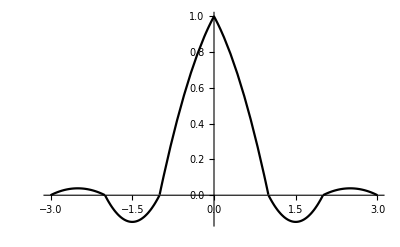

```mathematica
NSol=N[Sols[[1]]];
FullSol=Join[GenSol/.NSol,NSol]
fo[x_]:=f[x]/.FullSol;
Plot[fo[x],{x,-3,3},PlotStyle->Black,Background->White]
```